#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
(*Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]*)
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
ClearAll;
ImgSize=900;
SetDirectory["/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan/results

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];
parity="-";
jJ=1;
J0=1;
mJs=Range[-jJ,jJ,1];
thresholdLIT=10^(-8);
thresholdD=thresholdLIT;
mom=ReadList["kRange.dat",Number][[2]];
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
DNormHamMat=readREAL8list["./mat_np1^+"];
DBasisDim=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDim^2]],{DBasisDim,DBasisDim}];
DHam=ArrayReshape[DNormHamMat[[DBasisDim^2+1;;]],{DBasisDim,DBasisDim}];
```

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,0.2];
```

min/max: {1.60067×10^-9,10.5472}

(min/max) discarded elements: 28 {1.60067×10^-9,0.124671}

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

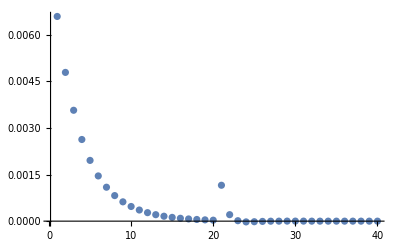

```mathematica
tv=Transpose[Eigensystem[DNorm]][[-2]];
ListPlot[Chop[DHam.tv[[2]],10^-6],PlotRange->Full]
```

#### The real calculation

Set a sensible cut-off

min/max: {1.60067×10^-9,10.5472}

(min/max) discarded elements: 2 {1.60067×10^-9,9.52404×10^-9}

B(D) = -2.22364

Dim_full^deuteron = 40=^!40   ;     Dim_(non - singular)^deuteron = 38

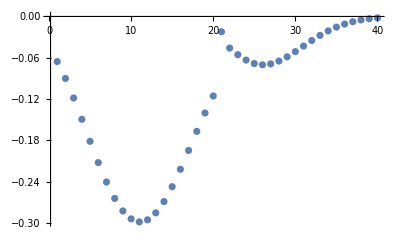

```mathematica
{DNmh,DNmhi}=matSqrts[DNorm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[DNmhi].DHam.DNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(D) = ",e0];
Print["Dim_full^deuteron = ",Dimensions[DNorm][[1]],"=^!",DBasisDim,"   ;     Dim_(non - singular)^deuteron = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[DNmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
(*LitNormHamMat=readREAL8list["./mat_0^-"];*)
LitNormHamMat=readREAL8list["./../LITstate/MATOUTB"];
LITbasisDim=IntegerPart[Sqrt[Length[LitNormHamMat] 0.5]];
LitNorm=ArrayReshape[LitNormHamMat[[1;;LITbasisDim^2]],{LITbasisDim,LITbasisDim}];LitHam=ArrayReshape[LitNormHamMat[[LITbasisDim^2+1;;]],{LITbasisDim,LITbasisDim}];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = 170

min/max: {-6.44378×10^-15,66.2341}

(min/max) discarded elements: 144 {-6.44378×10^-15,7.25758×10^-9}

0.0879799

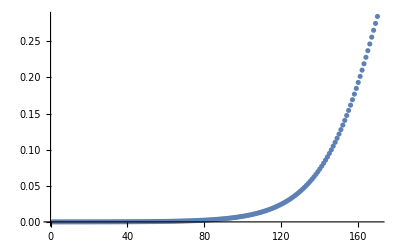

```mathematica
{LitNmh,LitNmhi}=matSqrts[LitNorm,thresholdLIT];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam.LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
e0l
fullv0l=Normalize[Transpose[LitNmh].v0l];
ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

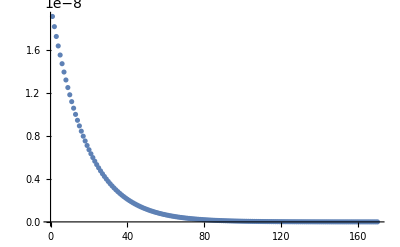

```mathematica
tv=Transpose[Eigensystem[LitNorm]][[-2]];
ListPlot[Chop[LitHam.tv[[2]],10^-16],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_inhomo*"],"_"][[All,1]]]];
ks=Range[0,nk];
mJ=mJs[[1]];
mL=mLs[[3]];
If[Abs[mJ-mL]≤1/2,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[mL]<>".log"&/@ks,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[-mL]<>".log"&/@ks
]

inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[DBasisDim+1;;,;;DBasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
CouplingBlock=ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}];

Print["Dim(⟨ψ|ο̂|deuteron⟩) = ",Dimensions[CouplingBlock]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

{./0_inhomo1-1_J1_mJ-1-mL-1.log,./1_inhomo1-1_J1_mJ-1-mL-1.log,./2_inhomo1-1_J1_mJ-1-mL-1.log,./3_inhomo1-1_J1_mJ-1-mL-1.log,./4_inhomo1-1_J1_mJ-1-mL-1.log,./5_inhomo1-1_J1_mJ-1-mL-1.log,./6_inhomo1-1_J1_mJ-1-mL-1.log,./7_inhomo1-1_J1_mJ-1-mL-1.log,./8_inhomo1-1_J1_mJ-1-mL-1.log}

Dim(⟨ψ|ο̂|deuteron⟩) = {170,40}

Dim(⟨ψ|Ĥ|ψ⟩) = {170,170}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {170,170}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],#[[1]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λsLit,trfLit,inhomo,egs,evgs},
OμRHS=normreg[thresholdD,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thresholdLIT,LITNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];

inhomo=(2/mom) (Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λsLit,(trfLit.inhomo)^2,egs}
];
Clear[litcomp];
litcomp[thresholdD_,thresholdLIT_,DNorm_,DHam_,LITNorm_,LITHam_,LITYD_]:=Block[{λscf=decompose[thresholdD,thresholdLIT,DNorm,DHam,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/((#[[1]]-egrnd-σRe)^2+σI^2))&/@tmpp)];
```

```mathematica
Clear[LIT,LITs,testfu];
LIT={};

Print["dim(cpl)=",Dimensions[CouplingBlock]];

minth=thresholdLIT;maxth=.0015 thresholdLIT;nth=3;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

testfu=Evaluate[litcomp[#,#,DNorm,DHam,LitNorm,LitHam,CouplingBlock]&/@thresholdrng];
LITs=(-1)^(jJ-J0) testfu/.σRe->σRs;

thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);
plote=ListPlot[Transpose[{σRs,#}]&/@LITs,
PlotLabel->Style["σ_I = "<>ToString[σI],18,Red],
AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},
PlotLegends->Placed[thrlegend,Above],
LabelStyle->12,ImageSize->ImgSize,PlotRange->Full,
Mesh->5,MeshFunctions->{#2&,#2&,#2&},PlotMarkers->{Automatic,Scaled[0.02 #]}&/@Range[1,nth],
Joined->True];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

dim(cpl)={170,40}

E_0( th=1.×10^-8 ) = -2.22364    dim(D,LIT) = {38}{26}

E_0( th=6.67167×10^-9 ) = -2.22397    dim(D,LIT) = {39}{27}

E_0( th=3.34333×10^-9 ) = -2.22397    dim(D,LIT) = {39}{27}

E_0( th=1.5×10^-11 ) = -2.22415    dim(D,LIT) = {40}{33}

plot.pdf

E_0( th=1.×10^-8 ) = -2.22364    dim(D,LIT) = {38}{26}

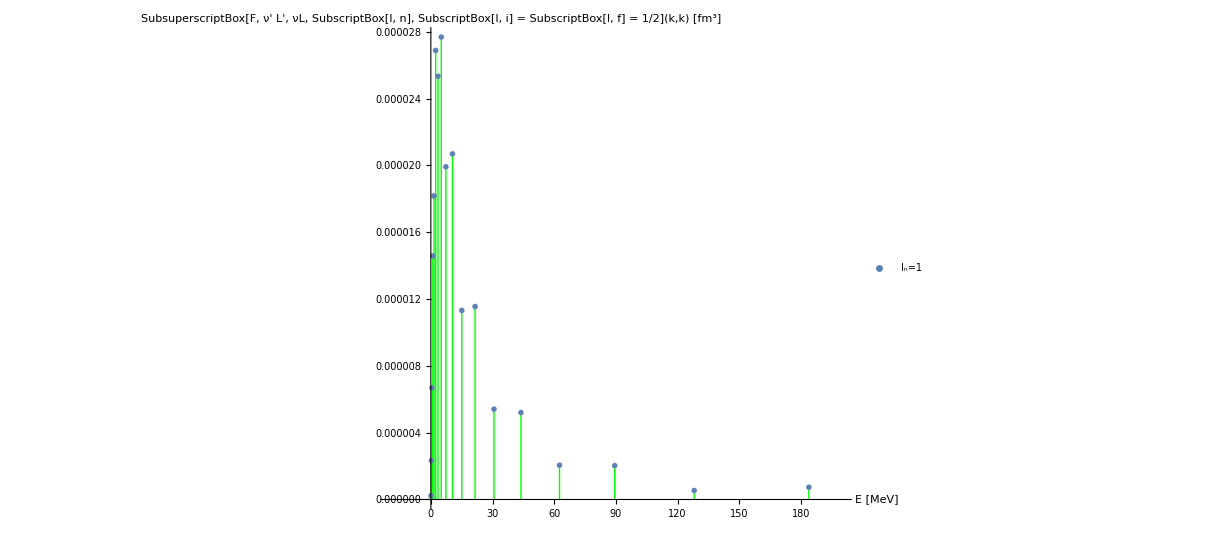

```mathematica
Clear[thresh,es,μ,transf];

thresh=thresholdD;
es=Eigensystem[DNorm];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresh&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];

esl=Eigensystem[LitNorm];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresh&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λsLit]];

inhomo=(Transpose[OμLHS].(CouplingBlock.OμRHS)).(evgs);
lpsi=Transpose[{λsLit,(trfLit.inhomo)^2}];

ListPlot[lpsi,Joined->False,PlotMarkers->{♪,12},Filling->Axis,FillingStyle->Green,PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->{},PlotLegends->{"I_n="<>ToString[jJ]},ImageSize->ImgSize]
```

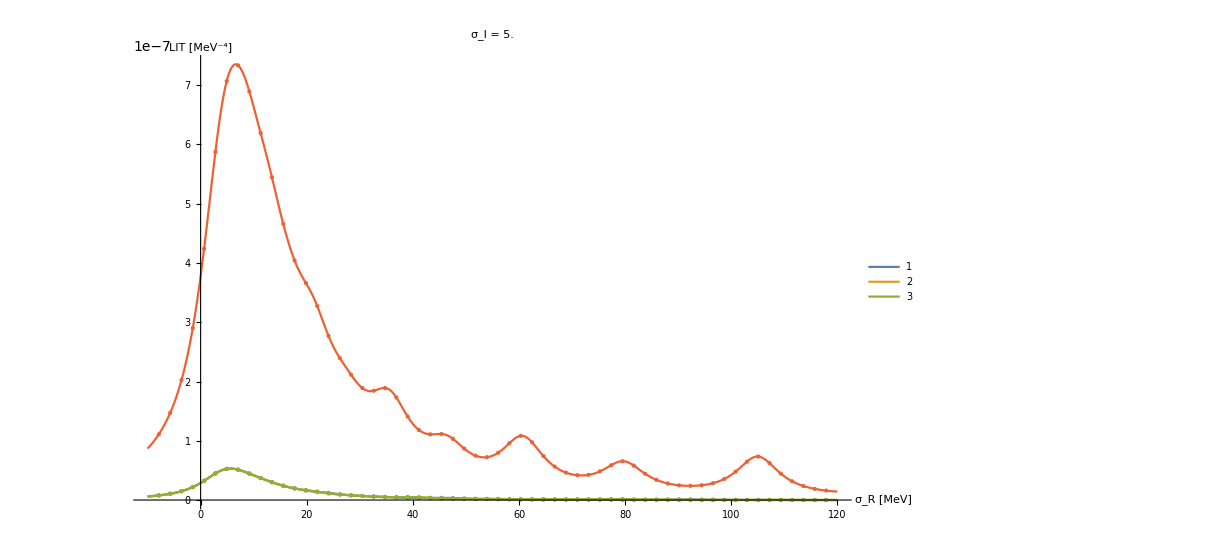

```mathematica
dimens=Length[#]&/@LIT[[All,2]];
Plot[testfu,{σRe,-10,120},PlotRange->{Automatic,Full},MaxRecursion->0,PlotPoints->500,MeshFunctions->{#&},Mesh->60,MeshStyle->PointSize[Large],
PlotLabel->Style["σ_I = "<>ToString[σI],18,Red],AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},ImageSize->ImgSize,PlotLegends->{"1","2","3"},ImageSize->ImgSize]
```

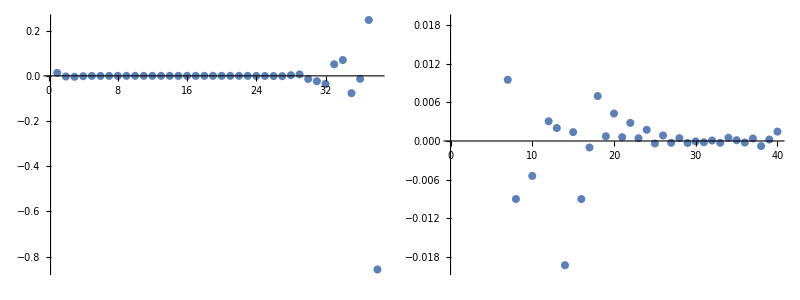

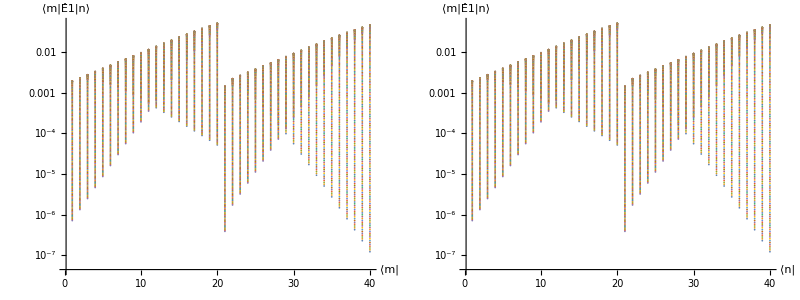

```mathematica
thrs=10^(-13);
OμRHS=normreg[thrs,DNorm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].DHam).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thrs,LitNorm];
{λsLit,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam).OμLHS];

inhomo=(Transpose[OμLHS].(CouplingBlock.OμRHS)).evgs;
Grid[{{ListPlot[inhomo,PlotRange->Full,ImageSize->ImgSize/2],ListPlot[evgs,ImageSize->ImgSize/2]}}]
Grid[{{ListLogPlot[Abs[CouplingBlock[[All,1;;]]],AxesLabel->{"⟨m|","⟨m|Ê1|n⟩"},ImageSize->ImgSize/2,PlotRange->Full,GridLines->{{},{1}}],ListLogPlot[Abs[CouplingBlock[[1;;,All]]],AxesLabel->{"⟨n|","⟨m|Ê1|n⟩"},ImageSize->ImgSize/2,PlotRange->Full,GridLines->{{},{1}}]}}]
```

```mathematica
(*DNorm//MatrixForm
LitNorm//MatrixForm
ndd=Sqrt[Dimensions[inhomos][[2]]];
ArrayReshape[inhomos,{ndd,ndd}]//MatrixForm
CouplingBlock//MatrixForm
CouplingBloxx//MatrixForm*)
```